Project A - Arjun Sekhar (Student ID: 18653508)

## Questions 1-10

# 7

Question: Plot the graphs of the functions 2 exp^(-x^-2)and Cos[Sin[x]+Cos[x]] between [-π, π]. Then find out the coordinates ‘x’ where they intersect.

```mathematica
(*Working*)
```

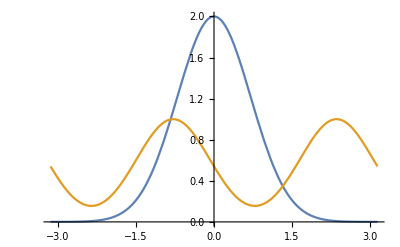

```mathematica
Plot[{2Exp[-x^2],Cos[Sin[x]+Cos[x]]},{x,-π,π}]
```

The first x-coordinate where the graph intersects is:

```mathematica
FindRoot[{2Exp[-x^2]-Cos[Sin[x]+Cos[x]]}==0,{x,-1.0}]
```

```mathematica
{x->-0.833970282003902}
```

The second x-coordinate where the graph intersects is:

```mathematica
FindRoot[{2Exp[-x^2]-Cos[Sin[x]+Cos[x]]}==0,{x,+1.4}]
```

```mathematica
{x->1.322272644290562}
```

```mathematica
(*Conclusion*)
```

Answer: Thus the x-coordinates of intersection are x=-0.83397 and x=1.32227

# 9

Question: Plot the graph Sin[x]^2-x^2 Cos[πx]-x in the range -3 ≤ x ≤3. Then find (numerically) all the roots of the equation Sin[x]^2-x^2 Cos[πx]-x=0 lying between -3 and 3.

```mathematica
(*Working*)
```

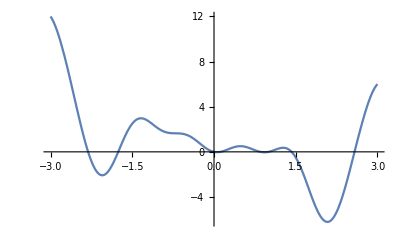

```mathematica
Plot[Sin[π x]^2-x^2 Cos[π x]-x,{x,-3,3}]
```

Thus the approximate roots of the graph Sin[π x]^2-x^2 Cos[π x]-x==0 are closest to:

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,-2.3}]
```

```mathematica
{x->-2.31034683286889529669040789048998271044}
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,-1.75}]
```

```mathematica
{x->-1.75741036008120810052446358895394951105}
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,0}]
```

```mathematica
{x->0}
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,1}]
```

```mathematica
{x->1.000000000}
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,1.4}]
```

```mathematica
{x->1.42392806378996726369664604446019059894}
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,2.6}]
```

```mathematica
{x->2.57928869158582306800560466163495775962}
```

However as we cannot visually see some of the roots, we find the roots between -0.3 and +0.3, and +0.6 and +1.6 	respectively, as separate graphs:

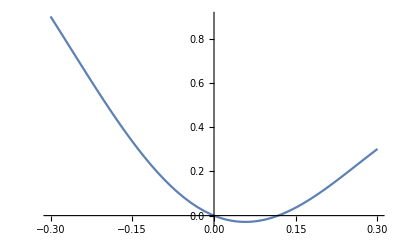

```mathematica
Plot[Sin[π x]^2-x^2 Cos[π x]-x,{x,-0.3,0.3}]
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,0.1}]
```

```mathematica
{x->0.1177102512270183636371365001878450552}
```

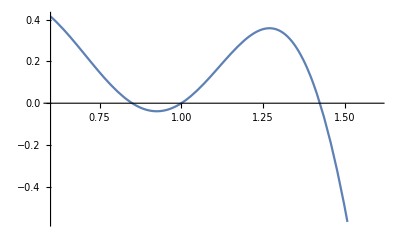

```mathematica
Plot[Sin[π x]^2-x^2 Cos[π x]-x,{x,0.6,1.6}]
```

```mathematica
FindRoot[{Sin[π x]^2-x^2 Cos[π x]-x}==0,{x,0.85}]
```

{x→0.849859}

```mathematica
{x->0.84985920164816432468342472460708092452}
```

```mathematica
(*Conclusion*)
```

Answer: The roots of the equation are x = -2.31034, x=-1.75741, x=0, x=0.11771, x=0.84985  x=1.00000, x=1.42392, x=2.57928.

## Question 11-20

# 15

Question: Show that ∑_(n=1)^89 1/(Cos[(n-1)°]Cos[(n)°])=Cos[1°]/Sin[1°]^2 where n° stands for ‘n’ degrees (as opposed to radians).

```mathematica
(*Working*)
```

Here it proves true that the left-hand side is equal to the right-hand side:

```mathematica
N[∑_(n=1)^89 1/(Cos[(n-1)°]Cos[(n)°])]==N[Cos[1°]/Sin[1°]^2]
```

```mathematica
True
```

This is the value for the left-hand side:

```mathematica
N[∑_(n=1)^89 1/(Cos[(n-1)°]Cos[(n)°])]
```

```mathematica
3282.6396655747767
```

This is the numerical value for the right had side (which is equal to the left-hand side):

```mathematica
N[Cos[1°]/Sin[1°]^2]
```

```mathematica
3282.6396655747767
```

```mathematica
(*Conclusion*)
```

Answer: In conclusion it can be confirmed that ∑_(n=1)^89 1/(Cos[(n-1)°]Cos[(n)°])=Cos[1°]/Sin[1°]^2 is a true statement.

# 18

Question: Show that among the first 450 Fibonacci numbers, the number of odd Fibonacci numbers is twice the number of even ones.

```mathematica
(*Working*)
```

```mathematica
Length[Select[Table[Fibonacci[i],{i,1,450}],OddQ]]
```

```mathematica
300
```

```mathematica
Length[Select[Table[Fibonacci[i],{i,1,450}],EvenQ]]
```

```mathematica
150
```

```mathematica
(*Conclusion*)
```

Answer: As it is proven in the statements above, the quantity of odd Fibonacci numbers is double the amount of even Fibonacci numbers, with 300 odd and 150 even.

## Question 21-30

# 23 (a)

Question: Show that among the fist 500 Fibonacci numbers, 18 of them are prime.

```mathematica
(*Working*)
```

This shows how, of the first 500 Fibonacci numbers, 18 of the are prime numbers:

```mathematica
Length[Select[Table[Fibonacci[i], {i,1,500}],PrimeQ]]
```

```mathematica
18
```

```mathematica
(*Conclusion*)
```

Answer: Thus it is proven from the above that there are 18 prime numbers between integers 1 - 500.

# 23 (b)

Question: Show that among the first 500 Fibonacci numbers, none of them is divisible by 350 and only one is divisible by 150.

```mathematica
(*Working*)
```

This shows no integers, out of the first 500 Fibonacci numbers, are divisible by 350:

```mathematica
Select[Table[Fibonacci[i], {i,1,500}], Divisible[#,350]&]
```

```mathematica
{}
```

This shows that only one integer out of the first 500 Fibonacci numbers is divisible by 150:

```mathematica
Select[Table[Fibonacci[i], {i,1,500}], Divisible[#,150]&]
```

```mathematica
{222232244629420445529739893461909967206666939096499764990979600}
```

```mathematica
(*Conclusion*)
```

Answer: While there are no integers between the first 500 Fibonacci numbers that are divisible by 350,however there is one integer divisible by 150 in the Fibonacci series and that is 222232244629420445529739893461909967206666939096499764990979600

# 26

```mathematica
(*Working*)
```

Question: Plot the graph of the ‘cowboy hat’ equation Sin[x^2+y^2]ⅇ^(-x^2)+Cos[x^2+y^2 ] as both ‘x’ and ‘y’ ranges from -2 to 2. Now plot the graph twice more, in each case changing the viewpoint o show the graph when it is viewed from above and below. What is the maximum value that the function takes in this range?

```mathematica
Plot3D[Sin[x^2+y^2] ⅇ^(-x^2)+Cos[x^2+y^2],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

This is the view of the cowboy hat from above:

```mathematica
Plot3D[Sin[x^2+y^2] ⅇ^(-x^2)+Cos[x^2+y^2],{x,-2,2},{y,-2,2}]
```

This is the view of the cowboy hat from below:

```mathematica
Plot3D[Sin[x^2+y^2] ⅇ^(-x^2)+Cos[x^2+y^2],{x,-2,2},{y,-2,2}]
```

```mathematica
NMaximize[Sin[x^2+y^2] ⅇ^(-x^2)+Cos[x^2+y^2],{x,y}]
```

```mathematica
{1.414213562373095,{x->1.6224826984216927598,y->-0.8862269254527598}}
```

```mathematica
(*Conclusion*)
```

Answer: The global maximum value of the function is 1.414213562373095.

## Questions 31-44

# 34

```mathematica
(*Working*)
```

Question: For 32 of the positive integers n between 1 and 100 the number n^2+n+1 is prime. Which ‘n’ are these? For how many of the positive integers ‘n’ between 1 and 100 000 is n^2+n+1 prime?

```mathematica
plist=Table[n^2+n+1,{n,1,100}]
```

```mathematica
{3,7,13,21,31,43,57,73,91,111,133,157,183,211,241,273,307,343,381,421,463,507,553,601,651,703,757,813,871,931,993,1057,1123,1191,1261,1333,1407,1483,1561,1641,1723,1807,1893,1981,2071,2163,2257,2353,2451,2551,2653,2757,2863,2971,3081,3193,3307,3423,3541,3661,3783,3907,4033,4161,4291,4423,4557,4693,4831,4971,5113,5257,5403,5551,5701,5853,6007,6163,6321,6481,6643,6807,6973,7141,7311,7483,7657,7833,8011,8191,8373,8557,8743,8931,9121,9313,9507,9703,9901,10101}
```

The above establishes the first n=100 integers that satisfy the equation n^2+n+1. Afterwards the ‘Select’ list below shows that out of the first 100 integers, there are 32 numbers that are prime:

```mathematica
Length[Select[plist, PrimeQ]]
```

```mathematica
{3,7,13,31,43,73,157,211,241,307,421,463,601,757,1123,1483,1723,2551,2971,3307,3541,3907,4423,4831,5113,5701,6007,6163,6481,8011,8191,9901}
```

Thus for numbers n between 1 and 100 000, we find which of the following values are prime:

```mathematica
Count[Table[PrimeQ[n^2+n+1],{n,1,100000}],True]
```

```mathematica
10751
```

```mathematica
(*Conclusion*)
```

Answer: Between 1 and 100 000,there are 10 751 positive integers that are prime.

# 41

Question: Let g[x]:=Sin[x]+Cos[x]. Plot graphs of g[g[g[g[x]]]] and g[g[g[g[g[x]]]]] for x lying between 0 and π. There are four points where the graphs cross. Find, numerically, their (x,y) coordinates.

```mathematica
(*Working*)
```

```mathematica
g[x_]:=Sin[x]+Cos[x]
```

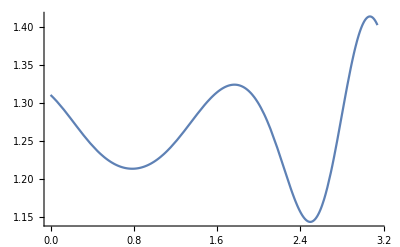

```mathematica
Plot[g[g[g[g[x]]]],{x,0,π}]
```

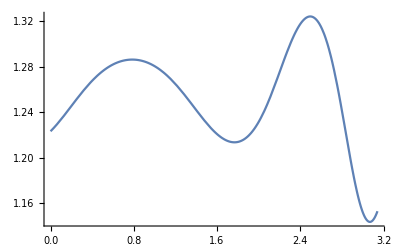

```mathematica
Plot[g[g[g[g[g[x]]]]],{x,0,π}]
```

```mathematica
{{Plot[{g[g[g[g[x]]]]==g[g[g[g[g[x]]]]]},{x,0,π},PlotLegends->"Expressions"]}, {□}}
```

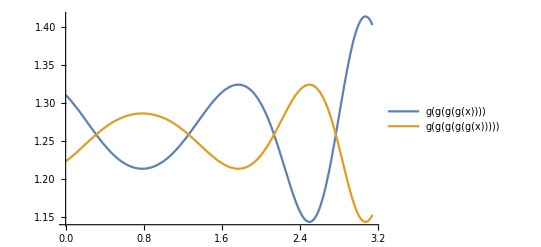

The x-coordinates of the intersection points are as follows (we enter the approximate values and then receive the more exact value for intersections):

```mathematica
g[x_]:=Sin[x]+Cos[x]
```

```mathematica
p={0.40,1.25,2.20,2.80}
```

```mathematica
{0.4,1.25,2.2,2.8}
```

```mathematica
FindRoot[g[g[g[g[x]]]]==g[g[g[g[g[x]]]]],{x,p}]
```

```mathematica
{x->{0.3120681493022201,1.2587281774926762,2.133697748134927,2.765564435000796}}
```

The y-coordinates of the intersection points are respectively as follows:

```mathematica
g[x_]:=Sin[x]+Cos[x]
```

```mathematica
g[g[g[g[g[0.31206814930222043]]]]]
```

```mathematica
1.2587281774926766
```

```mathematica
g[g[g[g[g[1.2587281774926766]]]]]
```

```mathematica
1.2587281774926764
```

```mathematica
g[g[g[g[g[2.1336977481349266]]]]]
```

```mathematica
1.2587281774926764
```

```mathematica
g[g[g[g[g[2.765564435000796]]]]]
```

```mathematica
1.2587281774926766
```

```mathematica
(*Conclusion*)
```

Answer: The common intersection coordinates of the following functions to 2 decimal places are [0.31, 1.26], [1.26, 1.26], [2.13, 1.26], [2.77, 1.26]